```mathematica
raw=OpenRead["C:\\Users\\anika_000\\Downloads\\reviews.csv"];
reviews=Map[StringSplit[#,"|"]&,ReadList[raw,String]];
DeleteDuplicates[Map[First[#]&,reviews]];
headers = reviews[[1]]
data = reviews[[1+ Range[Length@reviews -1]]];
positiveReviews=Select[reviews,#[[1]]=="positive"&];
negativeReviews=Select[reviews,#[[1]]=="negative"&];
randomPositiveReviews=RandomSample[positiveReviews,5000];
randomNegativeReviews=RandomSample[negativeReviews,5000];
randomPositiveLabels=randomPositiveReviews[[All,1]];
randomNegativeLabels=randomNegativeReviews[[All,1]];
randomPositiveTextReviews=randomPositiveReviews[[All,2]];
randomNegativeTextReviews=randomNegativeReviews[[All,2]];
```

{label,text}

```mathematica
prePositive=List[]; 
Do[PrependTo[prePositive,StringDelete[ToLowerCase[DeleteStopwords[randomPositiveTextReviews[[i]]]],RegularExpression["[\\.\"\',\!]"]]],{i,1,Length@randomPositiveTextReviews}];
prePositiveStem = WordStem[prePositive];
```

```mathematica
preNegative = List[];
Do[PrependTo[preNegative,StringDelete[ToLowerCase[DeleteStopwords[randomNegativeTextReviews[[i]]]],RegularExpression["[\\.\"\',\!]"]]],{i,1,Length@randomNegativeTextReviews}];
preNegativeStem = WordStem[preNegative];
preStem = Join[prePositiveStem, preNegativeStem];
```

```mathematica
featureSet=FeatureExtraction[preStem,"TFIDF"];
```

```mathematica
featureSetValues=featureSet[preStem];
```

```mathematica
dr=DimensionReduce[featureSetValues,100];
```

```mathematica
sentimentFeatureList=Classify["Sentiment",preStem,"Probabilities"];
sentimentProbabilities=Values[sentimentFeatureList];
```

```mathematica
finalFeatureSet = List[];
Do[PrependTo[finalFeatureSet, Join[dr[[i]],sentimentProbabilities[[i]]]],{i,1,Length@sentimentProbabilities}];
```

```mathematica
{}
```

{}

```mathematica
finalFeatureSet
```

{1}
 |  |  |  |

```mathematica
Dimensions[finalFeatureSet]
```

{10000,103}

```mathematica
positiveFeaturesTraining = finalFeatureSet[[1;;4000]];
```

```mathematica
negativeFeaturesTraining = finalFeatureSet[[5001;;9000]];
```

```mathematica
featuresTraining = Join[positiveFeaturesTraining, negativeFeaturesTraining];
```

```mathematica
positiveFeaturesTest= finalFeatureSet[[4001;;5000]];
negativeFeaturesTest = finalFeatureSet[[9001;;10000]];
featuresTest = Join[positiveFeaturesTest, negativeFeaturesTest];
labelTraining = Join[randomPositiveLabels[[1;;4000]], randomNegativeLabels[[1;;4000]]];
```

```mathematica
labelTest = Join[randomPositiveLabels[[4001;;5000]], randomNegativeLabels[[4001;;5000]]];
```

```mathematica
sentimentAnalysisRF=Classify[featuresTraining->labelTraining,Method->"RandomForest"];
```

```mathematica
cmRF=ClassifierMeasurements[sentimentAnalysisRF,featuresTest->labelTest];
```

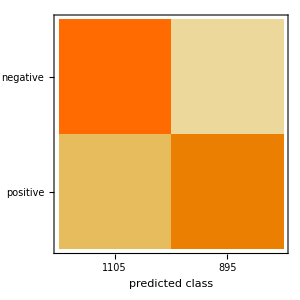
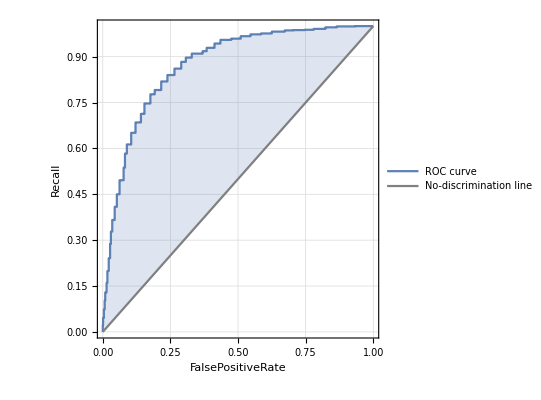
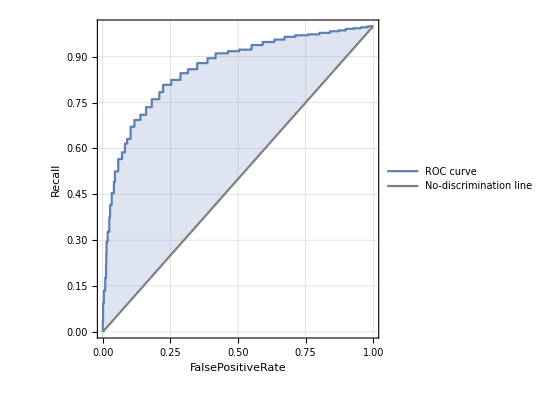
0.7875
<|negative→0.760181,positive→0.821229|>
<|negative→0.84,positive→0.735|>
-Graphics-
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
cmRF/@{"Accuracy","Precision","Recall",  "ConfusionMatrixPlot", "ROCCurve"}//TableForm
```

```mathematica
sentimentAnalysisNN=Classify[featuresTraining->labelTraining,Method->"NeuralNetwork"];
```

```mathematica
cmNN=ClassifierMeasurements[sentimentAnalysisNN,featuresTest->labelTest];
```

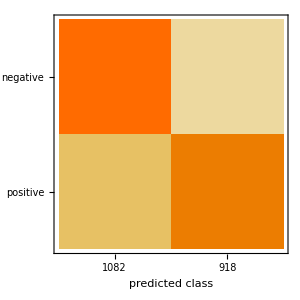
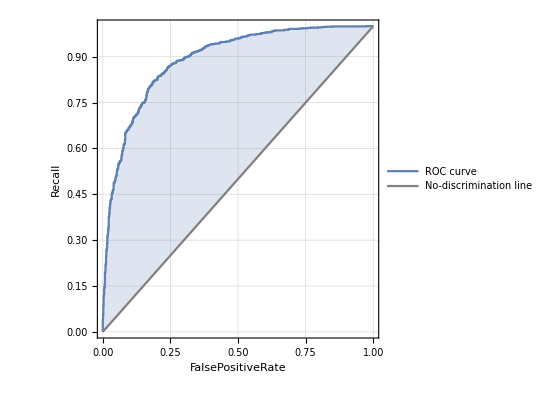
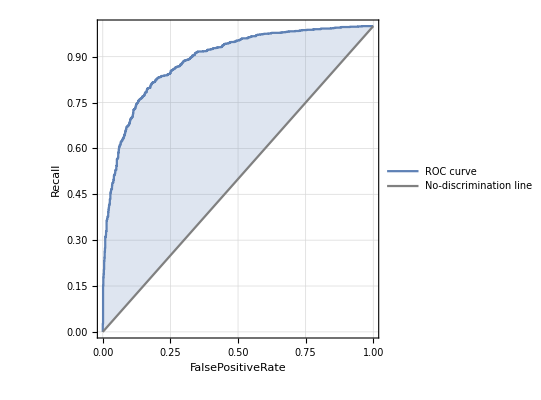
0.812
<|negative→0.788355,positive→0.839869|>
<|negative→0.853,positive→0.771|>
-Graphics-
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
cmNN/@{"Accuracy","Precision","Recall",  "ConfusionMatrixPlot", "ROCCurve"}//TableForm
```

```mathematica
sentimentAnalysisSVM=Classify[featuresTraining->labelTraining,Method->"SupportVectorMachine"];
```

```mathematica
cmSVM=ClassifierMeasurements[sentimentAnalysisSVM,featuresTest->labelTest];
```

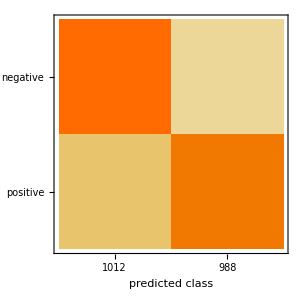
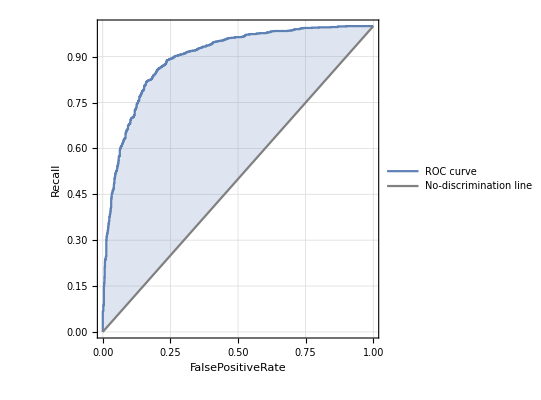
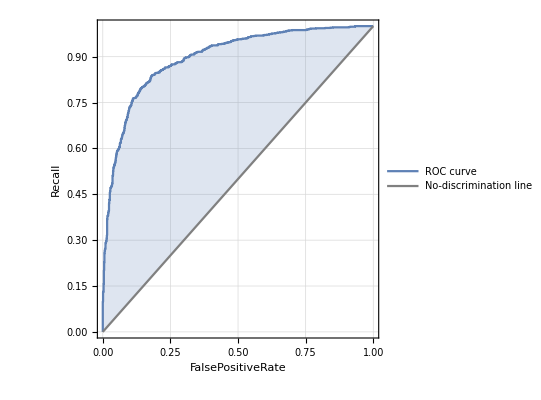
0.823
<|negative→0.81917,positive→0.826923|>
<|negative→0.829,positive→0.817|>
-Graphics-
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
cmSVM/@{"Accuracy","Precision","Recall",  "ConfusionMatrixPlot", "ROCCurve"}//TableForm
```